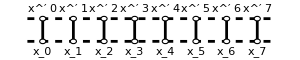

```mathematica
Graphics[{{AbsoluteThickness[2],Table[Line[{{x,1},{x,2}}],{x,8}]},{AbsoluteThickness[2],Dashed,Table[Line[{{0.5,y},{8.5,y}}],{y,2}]},{White,EdgeForm[Black],Table[Disk[{x,y},0.1],{x,8},{y,2}]},Table[Text["\!\(x\_"<>ToString[x-1]<>"\)",{x,0.8},{0,0.5}],{x,1,8}],Table[Text["\!\(x\^′\%"<>ToString[x-1]<>"\)",{x,2.2},{0,-0.5}],{x,1,8}]},ImageSize->300]
```

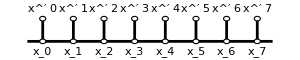

```mathematica
Graphics[{{AbsoluteThickness[2],Table[Line[{{x,1},{x,2}}],{x,8}]},{AbsoluteThickness[2],Table[Line[{{0.5,y},{8.5,y}}],{y,1}]},{White,EdgeForm[Black],Table[Disk[{x,y},0.1],{x,8},{y,2}]},Table[Text["\!\(x\_"<>ToString[x-1]<>"\)",{x,0.8},{0,0.5}],{x,1,8}],Table[Text["\!\(x\^′\%"<>ToString[x-1]<>"\)",{x,2.2},{0,-0.5}],{x,1,8}]},ImageSize->300]
```